ILUM = (∫^∞)_e_th de 1/((σ_r-e)^2+σ_i^2)·1/((a_n-e)^2+b_n^2)

```mathematica
ClearAll;
v18uixpath="/home/kirscher/kette_repo/ComptonLIT/v18uix_helium3/";
jlit=0.5;
dataCrossLitfull=N[ToExpression[Import[v18uixpath<>"real_LIT_J_"<>ToString[jlit],"Table","FieldSeparators"->" ; "]]];
dataCrossLit=N[ToExpression[Import[v18uixpath<>"real_LIT_J_"<>ToString[jlit],"Table","FieldSeparators"->" ; "]]][[2;;110]];
datamax=Sort[dataCrossLit,#1[[2]]>#2[[2]]&][[1]];

Lorentz[e_,a_,b_,c_]:=c/((a-e)^2+b^2);

ILanaPlus[sr_,si_,a_,b_,eth_,c_]:=c^2/(((sr-a)^2+(si-b)^2) ((sr-a)^2+(si+b)^2)) (((sr-a)^2+b^2-si^2)/si (Pi/2+ArcTan[(sr-eth)/si])+((sr-a)^2-b^2+si^2)/b (Pi/2+ArcTan[(a-eth)/b])+(sr-a) Log[((sr-eth)^2+si^2)/((a-eth)^2+b^2)])
LorentzPlus[e_,a_,b_,eth_,c_]:=HeavisideTheta[e-eth] c^2/((a-e)^2+b^2);

ILanaMinus[sr_,si_,a_,b_,eth_,c_]:=c/(((sr-a)^2+(si-b)^2) ((sr-a)^2+(si+b)^2)) (((sr-a)^2+b^2-si^2)/si (Pi/2-ArcTan[(sr-eth)/si])+((sr-a)^2-b^2+si^2)/b (Pi/2-ArcTan[(a-eth)/b])-(sr-a) Log[((sr-eth)^2+si^2)/((a-eth)^2+b^2)])
LorentzMinus[e_,a_,b_,eth_,c_]:=HeavisideTheta[eth-e] c/((a-e)^2+b^2);

ILnumPlus[sr_,si_,a_,b_,eth_]:=NIntegrate[Lorentz[e,sr,si,1.0] LorentzPlus[e,a,b,eth,1.0],{e,-Infinity,Infinity}]
ILnumMinus[sr_,si_,a_,b_,eth_]:=NIntegrate[Lorentz[e,sr,si,1.0] LorentzMinus[e,a,b,eth,1.0],{e,-Infinity,Infinity}]
```

Consistency between numerical and analytical integration

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {9.89546}. NIntegrate obtained 0.000717844 and 1.74535×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {9.89546}. NIntegrate obtained 0.000960472 and 2.47598×10^-6 for the integral and error estimates.

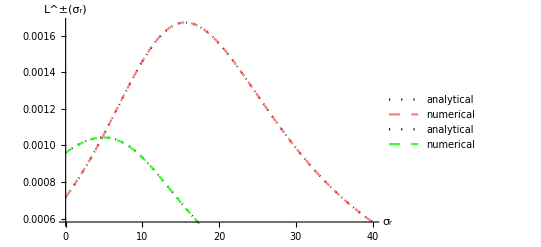

```mathematica
βtest=12.0;
γtest=12.0;
δtest=6.0;
ethtest=10;

obnd=40;
Show[
Plot[{ILanaPlus[α,βtest,γtest,δtest,ethtest,1.0],ILnumPlus[α,βtest,γtest,δtest,ethtest]},{α,0,obnd},PlotRange->Full,AxesLabel->{"σ_r","L^±(σ_r)"}, PlotStyle->{{Dotted,Black},{Red,Thick,Dashed,Opacity[0.5]}},PlotLegends->{"analytical","numerical"}],
Plot[{ILanaMinus[α,βtest,γtest,δtest,ethtest,1.0],ILnumMinus[α,βtest,γtest,δtest,ethtest]},{α,0,obnd}, PlotStyle->{{Dotted,Black},{Dashed,Thick,Green,Opacity[0.8]}},PlotLegends->{"analytical","numerical"}]
]
```

Fit model to “toy” LIT

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

FindFit::nrlnum: The function value … is not a list of real numbers with dimensions {109} at {abrute[1],abrute[2],abrute[3],abrute[4],abrute[5],abrute[6],abrute[7],abrute[8],abrute[9],abrute[10],abrute[11],abrute[12],abrute[13],abrute[14],abrute[15]} = {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}.

Part::partd: Part specification sigmaR⟦1⟧ is longer than depth of object.

Part::partd: Part specification sigmaR⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindFit::fdssnv: Search specification abrute[1]→If[Abs[abrute[2]]>1/10000000000000000,Abs[{abrute[1],abrute[2],abrute[3],abrute[4],abrute[5],abrute[6],abrute[7],abrute[8],abrute[9],abrute[10],abrute[11],abrute[12],abrute[13],abrute[14],abrute[15]}⟦2⟧],0.] without variables should be a list with 1 to 4 elements.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fdssnv: Search specification abrute[1]→If[Abs[abrute[2]]>1/10000000000000000,Abs[{abrute[1],abrute[2],abrute[3],abrute[4],abrute[5],abrute[6],abrute[7],abrute[8],abrute[9],abrute[10],abrute[11],abrute[12],abrute[13],abrute[14],abrute[15]}⟦2⟧],0.] without variables should be a list with 1 to 4 elements.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fdssnv: Search specification abrute[1]→If[Abs[abrute[2]]>1/10000000000000000,Abs[{abrute[1],abrute[2],abrute[3],abrute[4],abrute[5],abrute[6],abrute[7],abrute[8],abrute[9],abrute[10],abrute[11],abrute[12],abrute[13],abrute[14],abrute[15]}⟦2⟧],0.] without variables should be a list with 1 to 4 elements.

General::stop: Further output of FindFit::fdssnv will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMaximize::nnum: The function value … is not a number at {eee} = {-0.829053}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

Fit_max  = {2.37875×10^-9,{e→4.25863}}

Fit_max  = {2.38001×10^-9,{e→4.2868}}

Fit_max  = {2.37975×10^-9,{e→4.27382}}

Fit_max  = {2.37976×10^-9,{e→4.26386}}

Fit_max  = {2.37886×10^-9,{e→4.25745}}

Fit_max  = {2.37982×10^-9,{e→4.251}}

Fit_max  = {2.37914×10^-9,{e→4.2663}}

Fit_max  = {2.37845×10^-9,{e→4.29098}}

Fit_max  = {2.37909×10^-9,{e→4.27135}}

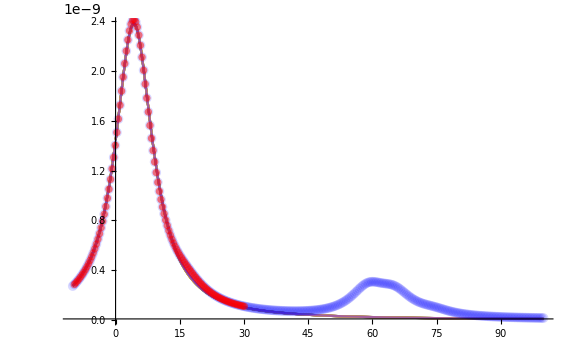
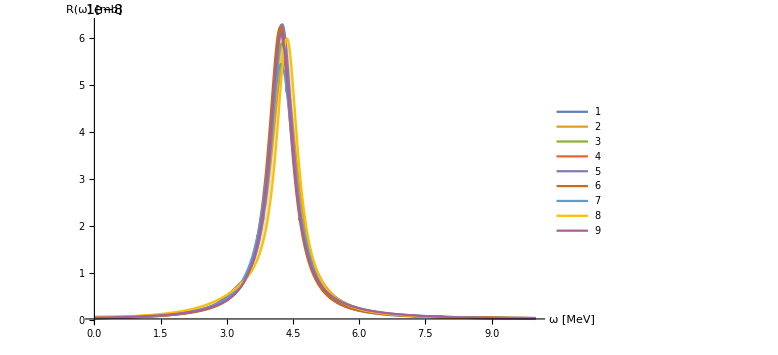
-Graphics- | -Graphics-

{0.+(1.96698×10^-20 HeavisideTheta[0.+e])/(1.23527+(0.433822-e)^2)+(2.17144×10^-25 HeavisideTheta[0.+e])/(0.202485+(3.29714-e)^2)+(7.9697×10^-18 HeavisideTheta[0.+e])/(0.33825+(3.9243-e)^2)+(2.05447×10^-9 HeavisideTheta[0.+e])/(2.87693+(3.92752-e)^2)+(3.11904×10^-24 HeavisideTheta[0.+e])/(0.417655+(4.1687-e)^2)+(6.00405×10^-9 HeavisideTheta[0.+e])/(0.0975558+(4.23345-e)^2)+(2.47757×10^-10 HeavisideTheta[0.+e])/(1.31169+(9.84627-e)^2),0.+(1.27653×10^-9 HeavisideTheta[0.+e])/(3.53503+(-0.953295-e)^2)+(5.58612×10^-21 HeavisideTheta[0.+e])/(2.1432+(-0.37015-e)^2)+(1.09748×10^-10 HeavisideTheta[0.+e])/(0.218725+(3.37504-e)^2)+(7.4053×10^-9 HeavisideTheta[0.+e])/(0.135766+(4.28649-e)^2)+(2.56698×10^-18 HeavisideTheta[0.+e])/(1.19749+(4.78184-e)^2),0.+(5.86005×10^-26 HeavisideTheta[0.+e])/(0.427791+(-0.655101-e)^2)+(8.41472×10^-10 HeavisideTheta[0.+e])/(0.765788+(3.78053-e)^2)+(5.71102×10^-9 HeavisideTheta[0.+e])/(0.101134+(4.2501-e)^2)+(1.96643×10^-9 HeavisideTheta[0.+e])/(1.29362+(4.55289-e)^2)+(1.47762×10^-25 HeavisideTheta[0.+e])/(1.8737+(5.41386-e)^2),0.+(8.60058×10^-32 HeavisideTheta[0.+e])/(0.526331+(-0.802322-e)^2)+(6.17386×10^-22 HeavisideTheta[0.+e])/(0.229221+(-0.789788-e)^2)+(2.70854×10^-10 HeavisideTheta[0.+e])/(0.43078+(3.60743-e)^2)+(5.90431×10^-9 HeavisideTheta[0.+e])/(0.095439+(4.23222-e)^2)+(1.45436×10^-9 HeavisideTheta[0.+e])/(3.26347+(4.57932-e)^2)+(4.99106×10^-10 HeavisideTheta[0.+e])/(3.20725+(8.97808-e)^2),0.+(2.12811×10^-23 HeavisideTheta[0.+e])/(0.244331+(-1.53515-e)^2)+(9.40133×10^-31 HeavisideTheta[0.+e])/(1.48381+(-1.52247-e)^2)+(4.11748×10^-29 HeavisideTheta[0.+e])/(0.646468+(2.60371-e)^2)+(2.81573×10^-28 HeavisideTheta[0.+e])/(2.35379+(3.06801-e)^2)+(3.50034×10^-10 HeavisideTheta[0.+e])/(0.179154+(3.21204-e)^2)+(5.91959×10^-9 HeavisideTheta[0.+e])/(0.0946454+(4.25505-e)^2)+(8.95558×10^-25 HeavisideTheta[0.+e])/(0.307225+(5.06576-e)^2)+(2.7591×10^-30 HeavisideTheta[0.+e])/(1.55475+(7.94685-e)^2)+(8.03134×10^-10 HeavisideTheta[0.+e])/(3.02702+(9.95804-e)^2),0.+(1.89208×10^-13 HeavisideTheta[0.+e])/(0.219037+(-1.49048-e)^2)+(2.81499×10^-26 HeavisideTheta[0.+e])/(0.896705+(-0.237143-e)^2)+(2.63406×10^-10 HeavisideTheta[0.+e])/(0.120542+(4.06645-e)^2)+(6.16025×10^-9 HeavisideTheta[0.+e])/(0.102263+(4.21114-e)^2)+(9.6338×10^-10 HeavisideTheta[0.+e])/(3.43829+(8.90917-e)^2),0.+(9.62074×10^-17 HeavisideTheta[0.+e])/(0.979584+(-0.673499-e)^2)+(4.44259×10^-12 HeavisideTheta[0.+e])/(0.133233+(3.6922-e)^2)+(7.61177×10^-9 HeavisideTheta[0.+e])/(0.140073+(4.23125-e)^2)+(4.57499×10^-22 HeavisideTheta[0.+e])/(0.411728+(4.27618-e)^2)+(5.00404×10^-29 HeavisideTheta[0.+e])/(0.115299+(4.74927-e)^2)+(4.22608×10^-10 HeavisideTheta[0.+e])/(2.81799+(7.40346-e)^2),0.+(6.69651×10^-14 HeavisideTheta[0.+e])/(1.14221+(-0.799405-e)^2)+(2.47827×10^-9 HeavisideTheta[0.+e])/(0.98246+(3.44407-e)^2)+(6.20049×10^-10 HeavisideTheta[0.+e])/(0.890159+(3.50267-e)^2)+(5.26918×10^-9 HeavisideTheta[0.+e])/(0.0907079+(4.36324-e)^2)+(2.7291×10^-11 HeavisideTheta[0.+e])/(1.5599+(5.00663-e)^2),0.+(2.77901×10^-10 HeavisideTheta[0.+e])/(0.976492+(-1.93992-e)^2)+(5.87567×10^-24 HeavisideTheta[0.+e])/(0.292493+(-0.626684-e)^2)+(6.04471×10^-9 HeavisideTheta[0.+e])/(0.100818+(4.22793-e)^2)+(4.71132×10^-22 HeavisideTheta[0.+e])/(1.2378+(4.47114-e)^2)+(2.8338×10^-9 HeavisideTheta[0.+e])/(3.16118+(4.80921-e)^2)}

{{abrute[1]→0.,abrute[2]→2.82307×10^-9,abrute[3]→0.,abrute[4]→0.0000157403,abrute[5]→0.,abrute[6]→0.0000774858,abrute[7]→0.,abrute[8]→4.65987×10^-13,abrute[9]→0.,abrute[10]→0.0000453262,abrute[11]→0.,abrute[12]→0.,abrute[13]→1.76608×10^-12,abrute[14]→1.40249×10^-10,abrute[15]→0.},{abrute[1]→0.0000860541,abrute[2]→1.60218×10^-9,abrute[3]→0.,abrute[4]→0.,abrute[5]→0.,abrute[6]→0.,abrute[7]→0.0000357286,abrute[8]→0.0000104761,abrute[9]→0.,abrute[10]→0.,abrute[11]→0.,abrute[12]→0.,abrute[13]→7.47404×10^-11,abrute[14]→0.,abrute[15]→0.},{abrute[1]→0.,abrute[2]→0.0000755713,abrute[3]→0.,abrute[4]→0.,abrute[5]→0.,abrute[6]→0.0000290081,abrute[7]→0.,abrute[8]→0.,abrute[9]→2.42075×10^-13,abrute[10]→3.84398×10^-13,abrute[11]→0.,abrute[12]→0.,abrute[13]→0.,abrute[14]→0.0000443444,abrute[15]→0.},{abrute[1]→0.,abrute[2]→0.,abrute[3]→0.0000164576,abrute[4]→0.,abrute[5]→0.,abrute[6]→2.93267×10^-16,abrute[7]→0.,abrute[8]→0.0000381361,abrute[9]→0.,abrute[10]→0.,abrute[11]→0.,abrute[12]→2.48473×10^-11,abrute[13]→0.0000223407,abrute[14]→0.,abrute[15]→0.0000768395},{abrute[1]→0.,abrute[2]→0.0000187092,abrute[3]→9.46339×10^-13,abrute[4]→0.,abrute[5]→0.,abrute[6]→1.67801×10^-14,abrute[7]→0.0000283396,abrute[8]→9.69605×10^-16,abrute[9]→0.,abrute[10]→0.0000769389,abrute[11]→4.61315×10^-12,abrute[12]→1.66105×10^-15,abrute[13]→6.41676×10^-15,abrute[14]→0.,abrute[15]→0.},{abrute[1]→0.,abrute[2]→4.3498×10^-7,abrute[3]→1.67779×10^-13,abrute[4]→0.,abrute[5]→0.0000162298,abrute[6]→0.,abrute[7]→0.,abrute[8]→0.,abrute[9]→0.0000310384,abrute[10]→0.,abrute[11]→0.,abrute[12]→0.,abrute[13]→0.,abrute[14]→0.,abrute[15]→0.0000784873},{abrute[1]→0.,abrute[2]→7.07392×10^-15,abrute[3]→0.,abrute[4]→9.80854×10^-9,abrute[5]→0.,abrute[6]→0.,abrute[7]→0.,abrute[8]→0.0000205574,abrute[9]→0.0000872455,abrute[10]→0.,abrute[11]→0.,abrute[12]→0.,abrute[13]→0.,abrute[14]→2.10775×10^-6,abrute[15]→2.13892×10^-11},{abrute[1]→0.,abrute[2]→0.,abrute[3]→0.,abrute[4]→0.,abrute[5]→0.0000249008,abrute[6]→0.,abrute[7]→0.,abrute[8]→2.58776×10^-7,abrute[9]→0.,abrute[10]→0.,abrute[11]→0.0000497822,abrute[12]→0.0000725891,abrute[13]→5.22408×10^-6,abrute[14]→0.,abrute[15]→0.},{abrute[1]→0.,abrute[2]→0.0000166704,abrute[3]→0.0000777478,abrute[4]→0.0000532334,abrute[5]→0.,abrute[6]→0.,abrute[7]→0.,abrute[8]→0.,abrute[9]→2.17056×10^-11,abrute[10]→0.,abrute[11]→0.,abrute[12]→2.42398×10^-12,abrute[13]→0.,abrute[14]→0.,abrute[15]→0.}}

```mathematica
si=5;smin=-10;smax=100;
peakth=0.35 10^-10;locth=10^-1;
randdim=15;desiredclusteranzahl=20;

litfitList={};lorentzbasplusList={};

Monitor[i=0;
While[Length[litfitList]<9,

peakmatch=False;

While[peakmatch==False,

(*lorentzCenters=RandomVariate[NormalDistribution[Random[Real,{-4,4}],Random[Real,{3,6}]],randdim];
lorentzWidths=Select[Abs[RandomVariate[NormalDistribution[Random[Real,{0.1,1.0}],Random[Real,{0.3,0.6}]],randdim]],((#1>0.3)&&(#1<2.2))&];
basTUPLES=Tuples[{lorentzCenters,lorentzWidths,lorentzThresholds}];
lorentzbasplus=RandomChoice[basTUPLES,desiredclusteranzahl];*)
lorentzbasplus=Table[{RandomReal[{-2,10}],RandomReal[{0.3,1.9}],0.0},{n,randdim}];


brutedimp=Length[lorentzbasplus];
Clear[abrute];coeffsb=Array[abrute,brutedimp];

LinearLorentzModelb=Sum[ILanaPlus[sigmaR,si,lorentzbasplus[[i]][[1]],lorentzbasplus[[i]][[2]],lorentzbasplus[[i]][[3]],coeffsb[[i]]],{i,brutedimp}];

modelLorentzABCpm=FindFit[dataCrossLit,LinearLorentzModelb,coeffsb,sigmaR,MaxIterations->2000,PrecisionGoal->12,AccuracyGoal->12,Method->Automatic];
(*optPOSsol=Map[Rule[#[[1]],Abs[#[[2]]]]&,modelLorentzABCpm];*)
optPOSsol=Map[Rule[#[[1]],If[Abs[#[[2]]]>10^-16,Abs[#[[2]]],0.0]]&,modelLorentzABCpm];

expan[x_]:=LinearLorentzModelb/.optPOSsol/.sigmaR->x;
modmax=Maximize[expan[eee],eee];
(*If[modmax[[1]]<0||modmax[[2]][[1]][[2]]<0,modmax={10^6,10^6}];*)
peakdiff=Abs[modmax[[1]]-datamax[[2]]];locdiff=Abs[modmax[[2]][[1]][[2]]-datamax[[1]]];

If[((peakdiff<peakth)&&(locdiff<locth)),{peakmatch=True;AppendTo[litfitList,optPOSsol];AppendTo[lorentzbasplusList,lorentzbasplus]},peakmatch=False];

];

Print["Fit_max  = "<>ToString[Maximize[expan[e],e],TraditionalForm]];
(*Print["Δ_max    = "<>ToString[peakdiff,TraditionalForm]];*)

];i,i--];

cycl=Table[Rule[n,{n+1}],{n,Length[litfitList]-1}];
plotlistRESPONSE=Table[(Sum[LorentzPlus[e,lorentzbasplusList[[n]][[m]][[1]],lorentzbasplusList[[n]][[m]][[2]],lorentzbasplusList[[n]][[m]][[3]],coeffsb[[m]]],{m,brutedimp}])/.litfitList[[n]],{n,Length[litfitList]}];
plotlistLIT=Table[Sum[ILanaPlus[sigmaR,si,lorentzbasplusList[[n]][[i]][[1]],lorentzbasplusList[[n]][[i]][[2]],lorentzbasplusList[[n]][[i]][[3]],coeffsb[[i]]],{i,brutedimp}]/.litfitList[[n]]/.sigmaR->x,{n,Length[litfitList]}];

Grid[{{
Show[
Plot[plotlistLIT,{x,smin,smax},PlotRange->Full,PlotPoints->40,ImageSize->Large,Filling->cycl],
ListPlot[dataCrossLitfull,PlotStyle->{Blue,Opacity[0.15],Large},PlotRange->Full, PlotMarkers->{Automatic, Medium},AxesLabel->{"σ_r [MeV]","L(σ) [mb·MeV^-1]"}],
ListPlot[dataCrossLit,PlotStyle->{Red,Opacity[0.5],Medium}]
],
Plot[plotlistRESPONSE,{e,0,10},PlotRange->Full,PlotLegends->Automatic,Filling->cycl,AxesLabel->{"ω [MeV]","R(ω) [mb]"},
ImageSize->Large]}}]
plotlistRESPONSE
litfitList
```